```mathematica
(*g:=2
β:=1/(300 * 8.617*10^-5) 
hbar:= 1.0545718×10-34*)
ϵ[n_]:=(hbar*π)^2/(2*m*L^2)*n^2

f[n_]:=4*π*n^2 * (g*ϵ[n])/(Exp[β*ϵ[n]]-1)


U = 1/8*Integrate[f[n], {n, 0, ∞}]
```

ConditionalExpression[(3 g hbar^2 Zeta[5/2])/(4 √2 L^2 m π^(3/2) ((hbar^2 β)/(L^2 m))^(5/2)),Re[(hbar^2 β)/(L^2 m)]>0]

```mathematica
b = 2
```

2

```mathematica
b
```

2

```mathematica
(π^3*hbar^2)/(4*m*L^2)Integrate[n^4/Exp[β*(n*π*hbar)^2/(2*m*L^2)], {n, 0, ∞}]
```

ConditionalExpression[(3 hbar^2)/(4 √2 L^2 m π^(3/2) ((hbar^2 β)/(L^2 m))^(5/2)),Re[(hbar^2 β)/(L^2 m)]>0]

```mathematica
(* 3D *) 
me= 9.10938*10^-31
mp = 1.6726219*10^-27
G = 6.67408*10^-11
h = 6.626070040*10^-34

Rc[M_]:=((2*0.0086*h^2*M^(5/3))/(me * mp^(5/3)))*(5/(3*G*M^2))

Rc[2*10^30]
```

9.10938×10^-31

1.67262×10^-27

6.67408×10^-11

6.62607×10^-34

6.97166×10^6

```mathematica
(3*2*10^30)/(4*π*(Rc[2*10^30])^3)
```

1.40907×10^9

```mathematica
4

k=1.38*10^-23


(3.14*2*π*k)/h^2
```

4

1.38×10^-23

6.20121×10^44

```mathematica
mhe = 6.646*10^-27
rho = 145

h^2/(2*π*k)*0.527*1/mhe*(rho/mhe)^(2/3)
```

6.646×10^-27

145

3.13503

```mathematica
mh := 1.67*10^-27
hbar := 1.05*10^-34

hbar^2/(2mh)*(3*π^2*(1.4*10^9)/mh)^(2/3)
```

2.8088×10^-17

```mathematica
2.8*10^-17/k
```

2.02899×10^6

```mathematica
(* 3c *)

U[r_]:=1/r+1/r^2
```

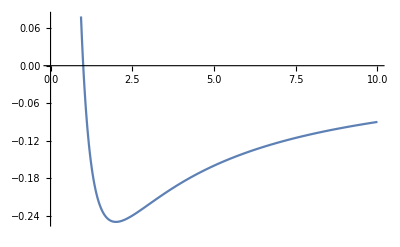

```mathematica
Plot[U[r], {r, 0, 10}]
```